```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for CA

>> <|chiSquared→1.40725×10^-6,rmsRelativeError→0.284809,rmsRelativeErrorDeaths→0.203207,rmsRelativeErrorPcr→0.33884,meanRelativeErrorDeaths→0.112089,meanRelativeErrorPcr→0.11353,rSquaredDeaths→0.00142509,rSquaredPcr→0.00971033,deathResidual7Day→2.77576,pcrResidual7Day→49.4698|>

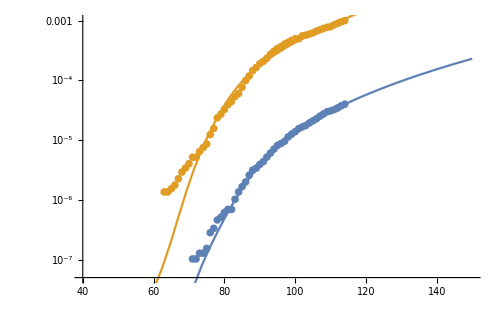
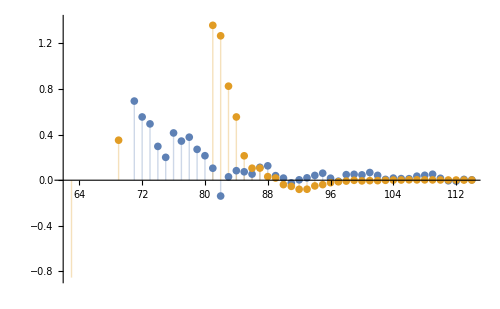
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.12493 | 0.0706725 | 58.3668 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[58.3668,92.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 48.1176 | 0.487856 | 98.6307 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[98.6307,92.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 0.677598 | 0.0229409 | 29.5367 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[29.5367,92.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.50029 | 0.0613415 | 24.458 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[24.458,92.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 4.74764×10^-9 | 1.18691×10^-9
Error | 92 | 3.18919×10^-11 | 3.46651×10^-13
Uncorrected Total | 96 | 4.77954×10^-9 | 
Corrected Total | 95 | 4.72048×10^-9 |

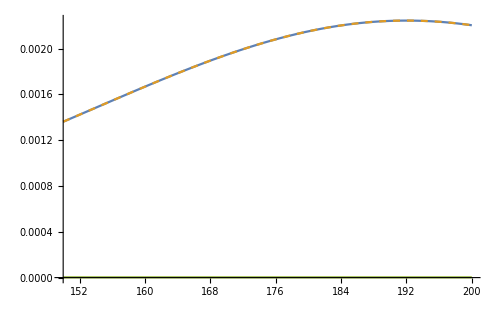
>> -Graphics-

>> Current Indefinite scenario Generating simulations for CA in the

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

NSum::nslim: Limit of summation {sSq[1.],sSq[2.],sSq[3.],sSq[4.],sSq[5.],sSq[6.],sSq[7.],sSq[8.],sSq[9.],sSq[10.]} is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

>> -Graphics-

>> -Graphics-

>> Current scenario Generating simulations for CA in the

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

>> -Graphics-

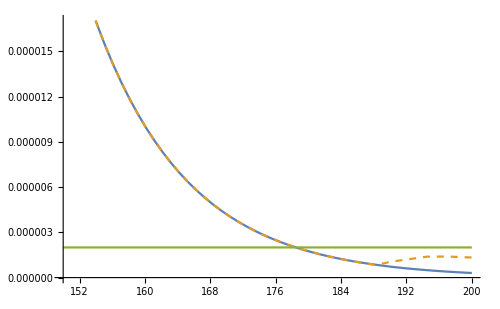
>> -Graphics-

>> Generating simulations for CA in the  Italy scenario

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

>> -Graphics-

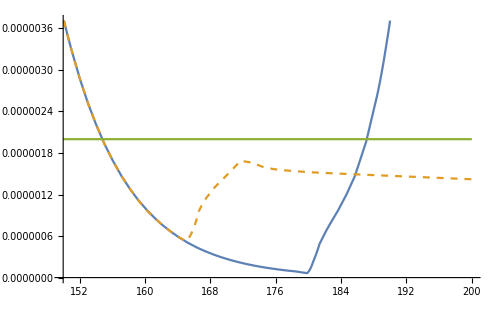
>> -Graphics-

>> Generating simulations for CA in the  Wuhan scenario

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

>> -Graphics-

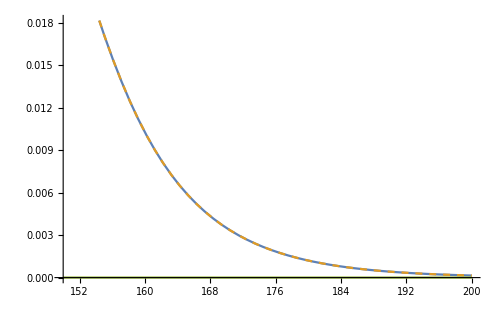
>> -Graphics-

>> Generating simulations for CA in the  Normal scenario

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

>> -Graphics-

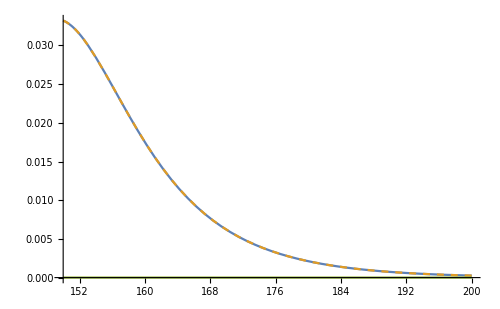
>> -Graphics-

>> Generating simulations for CA in the  Open May 1 scenario

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

>> -Graphics-

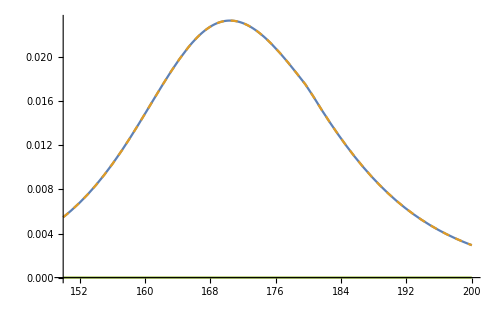
>> -Graphics-

>> Generating simulations for CA in the  Open Gradual May 1 scenario

>> <|r0natural→4.12493,importtime→48.1176,stateAdjustmentForTestingDifferences→0.677598,distpow→1.50029|>

>> -Graphics-

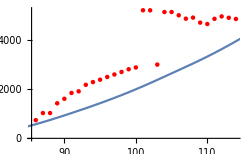
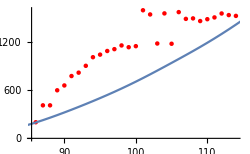
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

Export::jsonstrictencoding: Expression If cannot be exported as JSON.

General::stop: Further output of Export::jsonstrictencoding will be suppressed during this calculation.

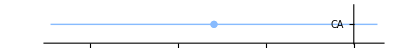
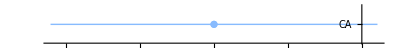
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | gradual | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfSymptomaticHospitalizedOrICU | fractionOfPCRHospitalized | fractionOfPCRHospitalizedOrICU | fractionHospitalizedInICU | fractionOfDeathInICU | fractionDeathOfHospitalizedOrICU | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences", "distpow"} |  |  |  | 
CA | 0.474762 | scenario5 | 614 | True | Current Indefinite | False | <|"totalProjectedDeaths" -> 48903.41397437981, "totalProjectedPCRConfirmed" -> 1.7936575352743613*^6, "totalProjectedInfected" -> 6.613611797766382*^6, "totalInfectedFraction" -> 0.1696544071746833, "fatalityRate" -> 0.007394358101105358, "fatalityRateSymptomatic" -> 0.010563368715864796, "fatalityRatePCR" -> 0.02726463274768862, "fractionOfSymptomaticHospitalized" -> 0.060493393197438745, "fractionOfSymptomaticHospitalizedOrICU" -> 0.08289247119881424, "fractionOfPCRHospitalized" -> 0.19027267743505288, "fractionOfPCRHospitalizedOrICU" -> 0.26072553712979984, "fractionHospitalizedInICU" -> 0.2702184851945386, "fractionOfDeathInICU" -> 0.6464716747332748, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419775, "fractionOfInfectionsPCRConfirmed" -> 0.2712069577292296, "dateContained" -> "", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 100590. | 3.06184×10^6 | 1.01379×10^7 | 0.260061 | 0.00992217 | 0.0141745 | 0.0328529 | 0.0700301 | 0.0959603 | 0.204145 | 0.279734 | 0.270218 | 0.654166 | 0.159172 | 0.302018 |  |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029 | 
CA | 0.474762 | scenario1 | 90 | True | Current | False | <|"totalProjectedDeaths" -> 48908.57049135342, "totalProjectedPCRConfirmed" -> 1.8119373880959556*^6, "totalProjectedInfected" -> 6.896482520131776*^6, "totalInfectedFraction" -> 0.17691069408377935, "fatalityRate" -> 0.007091813884626346, "fatalityRateSymptomatic" -> 0.010131162692323352, "fatalityRatePCR" -> 0.026992417515457407, "fractionOfSymptomaticHospitalized" -> 0.05811486123725883, "fractionOfSymptomaticHospitalizedOrICU" -> 0.07963323276659119, "fractionOfPCRHospitalized" -> 0.1887110266099259, "fractionOfPCRHospitalizedOrICU" -> 0.2585856489667744, "fractionHospitalizedInICU" -> 0.27021848519453856, "fractionOfDeathInICU" -> 0.646442009182828, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419775, "fractionOfInfectionsPCRConfirmed" -> 0.2627335576950514, "dateContained" -> "", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 294129. | 9.23914×10^6 | 2.96436×10^7 | 0.760427 | 0.00992217 | 0.0141745 | 0.0318351 | 0.0700301 | 0.0959604 | 0.203047 | 0.27823 | 0.270218 | 0.654163 | 0.159172 | 0.311674 |  |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029 | 
CA | 0.2 | scenario2 | 90 | False | Italy | False | <|"totalProjectedDeaths" -> 6889.119357128193, "totalProjectedPCRConfirmed" -> 123922.41231128474, "totalProjectedInfected" -> 694951.4706970886, "totalInfectedFraction" -> 0.01782710920772638, "fatalityRate" -> 0.009913094147736513, "fatalityRateSymptomatic" -> 0.01416156306819502, "fatalityRatePCR" -> 0.055592198607489894, "fractionOfSymptomaticHospitalized" -> 0.070011573779288, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09593497828997638, "fractionOfPCRHospitalized" -> 0.21925224315805933, "fractionOfPCRHospitalizedOrICU" -> 0.3004354573389072, "fractionHospitalizedInICU" -> 0.2702184851945387, "fractionOfDeathInICU" -> 0.6541901079856645, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419777, "fractionOfInfectionsPCRConfirmed" -> 0.17831808052291945, "dateContained" -> "", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 308978. | 9.76595×10^6 | 3.11402×10^7 | 0.798817 | 0.00992217 | 0.0141745 | 0.0316383 | 0.0700301 | 0.0959604 | 0.202715 | 0.277774 | 0.270218 | 0.654163 | 0.159172 | 0.313613 |  |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029 | 
CA | 0.11 | scenario3 | 60 | False | Wuhan | False | <|"totalProjectedDeaths" -> 5773.748610172829, "totalProjectedPCRConfirmed" -> 102871.32799332938, "totalProjectedInfected" -> 615883.3719844164, "totalInfectedFraction" -> 0.015798829982438593, "fatalityRate" -> 0.009374743454380713, "fatalityRateSymptomatic" -> 0.013392490649115307, "fatalityRatePCR" -> 0.05612592665807934, "fractionOfSymptomaticHospitalized" -> 0.06932170564492562, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09498967052269713, "fractionOfPCRHospitalized" -> 0.21804945499432346, "fractionOfPCRHospitalizedOrICU" -> 0.2987873090378962, "fractionHospitalizedInICU" -> 0.27021848519453845, "fractionOfDeathInICU" -> 0.651107254246867, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419772, "fractionOfInfectionsPCRConfirmed" -> 0.16703053317038138, "dateContained" -> "Thu 4 Jun 2020 00:32:47", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 5773.75 | 102871. | 615883. | 0.0157988 | 0.00937474 | 0.0133925 | 0.0561259 | 0.0693217 | 0.0949897 | 0.218049 | 0.298787 | 0.270218 | 0.651107 | 0.159172 | 0.167031 | Thu 4 Jun 2020 00:32:47 |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029 | 
CA | 1 | scenario4 | 90 | False | Normal | False | <|"totalProjectedDeaths" -> 306245.4623395764, "totalProjectedPCRConfirmed" -> 8.988291108309986*^6, "totalProjectedInfected" -> 3.1214080133504428*^7, "totalInfectedFraction" -> 0.8007131991540902, "fatalityRate" -> 0.00981113206058762, "fatalityRateSymptomatic" -> 0.0140159029436966, "fatalityRatePCR" -> 0.034071600335289755, "fractionOfSymptomaticHospitalized" -> 0.06988694217613682, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09576419895311633, "fractionOfPCRHospitalized" -> 0.20757671410328823, "fractionOfPCRHospitalizedOrICU" -> 0.28443679360475743, "fractionHospitalizedInICU" -> 0.2702184851945385, "fractionOfDeathInICU" -> 0.6534827247739509, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419772, "fractionOfInfectionsPCRConfirmed" -> 0.28795630272833744, "dateContained" -> "", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 309835. | 8.99992×10^6 | 3.12266×10^7 | 0.801034 | 0.00992217 | 0.0141745 | 0.0344265 | 0.0700301 | 0.0959604 | 0.207852 | 0.284814 | 0.270218 | 0.654163 | 0.159172 | 0.288213 |  |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029 | 
CA | 0.474762 | scenario6 | 6 | True | 1 | Open May 1 | False | <|"totalProjectedDeaths" -> 303712.5129766, "totalProjectedPCRConfirmed" -> 9.22938679452549*^6, "totalProjectedInfected" -> 3.1171546173156142*^7, "totalInfectedFraction" -> 0.7996221049005513, "fatalityRate" -> 0.009743261091044201, "fatalityRateSymptomatic" -> 0.013918944415777429, "fatalityRatePCR" -> 0.03290711720487761, "fractionOfSymptomaticHospitalized" -> 0.06978338554100338, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09562229807863194, "fractionOfPCRHospitalized" -> 0.20575628842950963, "fractionOfPCRHospitalizedOrICU" -> 0.28194231322008506, "fractionHospitalizedInICU" -> 0.27021848519453856, "fractionOfDeathInICU" -> 0.65311434808401, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419775, "fractionOfInfectionsPCRConfirmed" -> 0.2960837022089562, "dateContained" -> "", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 309509. | 9.24967×10^6 | 3.11936×10^7 | 0.800189 | 0.00992217 | 0.0141745 | 0.0334616 | 0.0700301 | 0.0959604 | 0.20622 | 0.282577 | 0.270218 | 0.654163 | 0.159172 | 0.296524 |  |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029
CA | 0.474762 | scenario7 | 60 | True | 1 | Open Gradual May 1 | True | <|"totalProjectedDeaths" -> 263214.07106286456, "totalProjectedPCRConfirmed" -> 9.078587703430934*^6, "totalProjectedInfected" -> 2.9865282296119392*^7, "totalInfectedFraction" -> 0.7661134215292021, "fatalityRate" -> 0.008813379644399539, "fatalityRateSymptomatic" -> 0.012590542349142201, "fatalityRatePCR" -> 0.02899284334317683, "fractionOfSymptomaticHospitalized" -> 0.0676457430430261, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09269314400359746, "fractionOfPCRHospitalized" -> 0.19955207533151534, "fractionOfPCRHospitalizedOrICU" -> 0.27344084672343355, "fractionHospitalizedInICU" -> 0.2702184851945387, "fractionOfDeathInICU" -> 0.6490272920786954, "fractionDeathOfHospitalizedOrICU" -> 0.15917210011419777, "fractionOfInfectionsPCRConfirmed" -> 0.3039846606308683, "dateContained" -> "", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 299526. | 9.31479×10^6 | 3.01876×10^7 | 0.774381 | 0.00992217 | 0.0141745 | 0.032156 | 0.0700301 | 0.0959604 | 0.203711 | 0.27914 | 0.270218 | 0.654163 | 0.159172 | 0.308564 |  |  |  | 4.12493 | 48.1176 | 0.677598 | 1.50029

```mathematica
asd=GenerateModelExport[100,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```